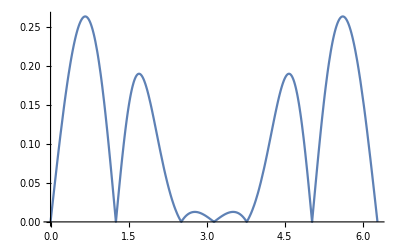

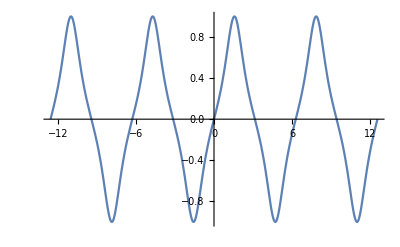

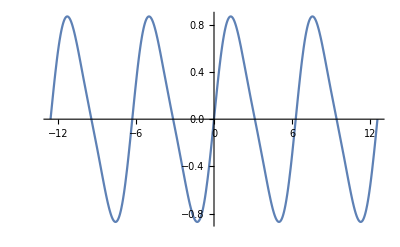

```mathematica
(*Да се построи тригонометричен полином от ред n=2 за f(x)= sin(x)/(1+cos(x)^2), с възлите Xk = 2*k*Pi/(2n+1)*)
n=2;
Do [x[k]=2*k*Pi/(2*n+1),{k,0,2n}];
f[t_]:=Sin[t]/(1+(Cos[t])^2);
l[k_,t_]:=Product[Sin[(t-x[j])/2]/Sin[(x[k]-x[j])/2],{j,0,k-1}]*Product[Sin[(t-x[j])/2]/Sin[(x[k]-x[j])/2],{j,k+1,2*n}];
T[t_]:=Sum[f[x[k]]*l[k,t],{k,0,2*n}];
Plot[Abs[f[t]-T[t]],{t,0,2*Pi}]
Plot[f[t],{t,-4*Pi,4*Pi}]
Plot[T[t],{t,-4*Pi,4*Pi}]
```